```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.3,Jtwo,2*0.3,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.5}]
```

{z→0.5}

```mathematica
Clear[IntPlus,NullsHolm,G,P,Inv]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))/.{J->1,q->0.3,l->2*0.3}
```

0.5+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
p= Check[FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
],z->0];
AppendTo[lst,{Jtwoo,p}];
,{n,1,199,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,200,1}];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.5]]
```

{{0.005,0.506138},{0.01,0.512055},{0.015,0.51775},{0.02,0.523225},{0.025,0.528481},{0.03,0.533517},{0.035,0.538333},{0.04,0.542928},{0.045,0.547302},{0.05,0.551452},{0.055,0.555378},{0.06,0.559078},{0.065,0.56255},{0.07,0.565792},{0.075,0.568803},{0.08,0.571581},{0.085,0.574123},{0.09,0.576429},{0.095,0.578497},{0.1,0.580325}}

```mathematica
moduler[Lister[-1,-0.005,0.5]]
```

{{-0.005,0.493638},{-0.01,0.487049},{-0.015,0.48023},{-0.02,0.473179},{-0.025,0.465889},{-0.03,0.458355},{-0.035,0.450571},{-0.04,0.44253},{-0.045,0.434221},{-0.05,0.425636},{-0.055,0.416761},{-0.06,0.407584},{-0.065,0.398088},{-0.07,0.388255},{-0.075,0.378062},{-0.08,0.367486},{-0.085,0.356496},{-0.09,0.345056},{-0.095,0.333126},{-0.1,0.320655}}

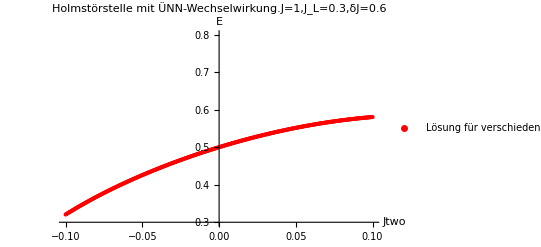

```mathematica
P = ListPlot[Fueger[moduler[Lister[1,0.0005,0.5]],moduler[Lister[-1,-0.0005,0.5]]],AxesLabel->{Jtwo,"E"},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.3,δJ=0.6",PlotRange->{0.3,0.8},PlotStyle->Red]
```

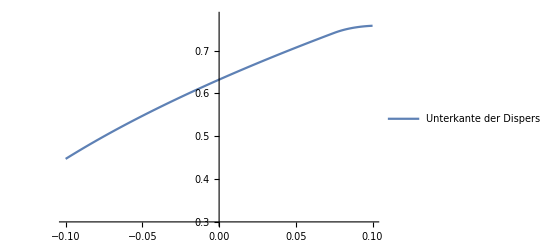

```mathematica
G = Plot[Sqrt[1+2*(0.3*Cos[Inv[0.3,Jtwo]]+Jtwo*Cos[2*Inv[0.3,Jtwo]])],{Jtwo,-0.1,0.1},PlotRange->{0.3,0.78},PlotLegends->{"Unterkante der Dispersion"}]
```

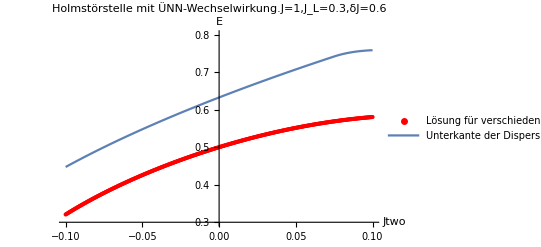

```mathematica
Show[P,G]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.0005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
differ[-1,0.3,moduler[Lister[-1,-0.005,0.5]]]
```

{{-0.005,0.130862},{-0.01,0.129393},{-0.015,0.128046},{-0.02,0.126821},{-0.025,0.125719},{-0.03,0.12474},{-0.035,0.123885},{-0.04,0.123156},{-0.045,0.122555},{-0.05,0.122087},{-0.055,0.121755},{-0.06,0.121566},{-0.065,0.121527},{-0.07,0.121647},{-0.075,0.121938},{-0.08,0.122412},{-0.085,0.123088},{-0.09,0.123985},{-0.095,0.125131},{-0.1,0.126558}}

```mathematica
differ[1,0.3,moduler[Lister[1,0.005,0.5]]]
```

{{0.005,0.134174},{0.01,0.13602},{0.015,0.137994},{0.02,0.1401},{0.025,0.142339},{0.03,0.144716},{0.035,0.147232},{0.04,0.149892},{0.045,0.152698},{0.05,0.155655},{0.055,0.158765},{0.06,0.162033},{0.065,0.165461},{0.07,0.169055},{0.075,0.754073},{0.08,0.175915},{0.085,0.177737},{0.09,0.178554},{0.095,0.178575},{0.1,0.177963}}

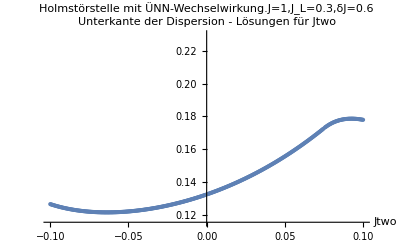

```mathematica
ListPlot[Fueger[differ[-1,0.3,moduler[Lister[-1,-0.0005,0.5]]],differ[1,0.3,moduler[Lister[1,0.0005,0.5]]]],AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.3,δJ=0.6"]
```